```mathematica
Clear["Global`*"]
```

## Load previous data

```mathematica
j=9;
(*LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation3/200x100/data";*)LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set1/finished_sims_A/data";
ρAll=Import[StringJoin[LoadFolder, "_rho_",ToString[j],".csv"]];
ϕAll=Import[StringJoin[LoadFolder, "_phi_",ToString[j],".csv"]];
VAll=Import[StringJoin[LoadFolder, "_V_",ToString[j],".csv"]];
```

```mathematica
Dimensions@VAll
```

{201,101}

```mathematica
Import[StringJoin[LoadFolder, "_parameters",ToString[j],".csv"]]
```

{{eO,1000},{eM,100},{η,25/9},{ξ,5/18},{τ,10},{D1,1000},{α,1/1000},{ρdA,0.0058},{ρdB,0.0076},{ρh,1/1000},{aρ,6},{a,6},{L,1500},{tmax,8},{Nx,200},{T,100}}

## Compute v and width for range of parameters (Automated pipeline)

```mathematica
counter=0; (*simulation counter *)
```

```mathematica
(* Parameters *)
(*params={eO->1000, eM->30, η->25/9, ξ->5/18, τ->10, D1->1000, α-> 1/1000, ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3), ρh->1*10^(-3), aρ-> 6,a->6}
L=1500;
tmax=8;*)
(*params={eO-> 1000, eM-> 30, η-> 25/9, ξ-> 5/18, τ-> 10, D1->15, α-> 2*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3),aρ->4,a->4,ρh->1*10^(-3)};*)
params={eO-> 1000, η-> 25/9, ξ-> 5/18, τ-> 10, D1->15, α-> 2*10^(-5), ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3),aρ->4,a->4,ρh->1*10^(-3)}
L=1500;
tmax=8;
```

{eO→1000,η→25/9,ξ→5/18,τ→10,D1→15,α→1/50000,ρdA→0.0058,ρdB→0.0076,aρ→4,a→4,ρh→1/1000}

```mathematica
counter = counter+1;
Print["Simulation", counter];
```

Simulation1

```mathematica
(* list of simulations *)
eMlist = {10}; (*{10,50,100,500};*)

(* list of simulations 
eMlist = {3,10,30,50,80,100,300, 500, 900}; *)
```

```mathematica
For[counter=1, counter≤ Length[eMlist], counter++,
Print["Simulation", counter];

(*AppendTo[params,eMlist[[counter]] ];*)
AppendTo[params,eM -> eMlist[[counter]]  ];

(* ICs and BCs *)
ρ0[x_]:=(Tanh[aρ x/L]+1)/2 (ρdA-ρdB)+ ρdB;
ϕ0[x_]:=(1-Tanh[a x/L])/2;
iv={ρ[x,0]==ρ0[x],ϕ[x,0]==ϕ0[x],v[x,0]==0} /. params;
(*iv={ρ[x,0]==ρ0[x],ϕ[x,0]==fData[x],v[x,0]==0} /. params;*)
bc={ρ[-L,t]==ρ0[-L],ρ[L,t]==ρ0[L],ϕ[-L,t]==ϕ0[-L],ϕ[L,t]==ϕ0[L],v[-L,t]==0,v[L,t]==0} /. params;
kA:= 1/τ((ρdA-ρ[x,t])/ρdA);
kB:=1/τ((ρdB-ρ[x,t])/ρdB);
e:= (eM(1-ϕ[x,t])+eO ϕ[x,t]) ; (* Stiffness *)
kD := α (e-eM);

(* Define PDE system*)
PDEsys={D[ρ[x,t],t]+D[ρ[x,t] (v[x,t]),x]==(kA (1-ϕ[x,t])+kB ϕ[x,t]) ρ[x,t],D[ϕ[x,t],t]+(v[x,t]) D[ϕ[x,t],x]==D1 D[ϕ[x,t],{x,2}]+ D1 D[ρ[x,t],x] D[ϕ[x,t],x]/ρ[x,t]+(kB-kA) ϕ[x,t] (1-ϕ[x,t])+kD (1-ϕ[x,t]),
ρ[x,t](η D[v[x,t],{x,2}]-ξ v[x,t])==e D[ρ[x,t],x] + D[e, x] Log[ρ[x,t]/ρh]*ρ[x,t]};
vars={ρ,ϕ,v};
fullsys=Simplify@Join[PDEsys/.params,bc,iv];

(* Discretize PDE*)
discretization1 = {ρ[x,t]-> Subscript[ρ, i,m], Derivative[1,0][ρ][x,t]-> (Subscript[ρ, i+1,m]-Subscript[ρ, i-1,m])/(2 Δx), ϕ[x,t]-> Subscript[ϕ, i,m], Derivative[1,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]-Subscript[ϕ, i-1,m])/(2 Δx),Derivative[2,0][ϕ][x,t]-> (Subscript[ϕ, i+1,m]- 2 Subscript[ϕ, i,m] + Subscript[ϕ, i-1,m])/(Δx)^2,
v[x,t]-> Subscript[v, i,m], Derivative[1,0][v][x,t]-> (Subscript[v, i+1,m]-Subscript[v, i-1,m])/(2 Δx),Derivative[2,0][v][x,t]-> (Subscript[v, i+1,m]- 2 Subscript[v, i,m] + Subscript[v, i-1,m])/(Δx)^2};
discretizationT={Derivative[0,1][ρ][x,t]->  (Subscript[ρ, i,m+1]-Subscript[ρ, i,m])/Δt, Derivative[0,1][ϕ][x,t]->  (Subscript[ϕ, i,m+1]-Subscript[ϕ, i,m])/Δt};
pdeDiscretized =PDEsys /.discretizationT /. discretization1;

(* Define mesh *)
Nx=200;
T= 100;
ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;
xmesh= Range[-L, L, ΔxSet];
tmesh =Range[0, tmax, tmax/T];
(*
Print[xmesh[[Nx/2+1]]];
Print[ N@ΔxSet]
Print[ N@ΔtSet]*)

(* Boundary conditions *)
ρL=ρ0[-L] /. params; ρR=ρ0[L] /. params; 
(*ϕL = 1; ϕR = 0;*)
ϕL = ϕ0[-L]/.params; ϕR = ϕ0[L]/.params;
VL = 0; VR = 0;
bcρ={Subscript[ρ, 0,m]==ρL,Subscript[ρ, Nx,m]==ρR};
bcϕ={Subscript[ϕ, 0,m]==ϕL,Subscript[ϕ, Nx,m]==ϕR};
bcV={Subscript[v, 0,m]==VL,Subscript[v, Nx,m]==VR};
bcρRepl={Subscript[ρ, 0,m]-> ρL,Subscript[ρ, Nx,m]->ρR};
bcϕRepl={Subscript[ϕ, 0,m]-> ϕL,Subscript[ϕ, Nx,m]->ϕR};
bcVRepl={Subscript[v, 0,m]-> VL,Subscript[v, Nx,m]->VR};

(* Initial conditions *)
ρ0Set=Table[ ρ0[ xmesh[[i]] ] /. params, {i,1,Nx+1}];
ϕ0Set=Table[Boole[(i<Nx/2)], {i, 0, Nx}];
ϕ0Set=Table[ ϕ0[xmesh[[i]]], {i,0, Nx}] /. params; 

(* Initialize values *)
ρAll=Table[Subscript[ρ, i,m], {i, 0, Nx}, {m, 0, T}];
ϕAll=Table[Subscript[ϕ, i,m], {i, 0, Nx}, {m, 0, T}];
VAll=Table[Subscript[v, i,m], {i, 0, Nx}, {m, 0, T}];

(* set initial values*)
Do[ρAll[[i+1, 1]] =ρ0Set[[i+1]], {i,0,Nx}]; 
Do[ϕAll[[i+1, 1]] =ϕ0Set[[i+1]], {i,0,Nx}]; 

(* set Dirichlet boundary values *)
Do[ρAll[[1, j+1]] = ρL, {j, 0, T}];
Do[ρAll[[Nx+1, j+1]] = ρR, {j, 0, T}];
Do[ϕAll[[1, j+1]] = ϕL, {j, 0, T}];
Do[ϕAll[[Nx+1, j+1]] = ϕR, {j, 0, T}];
Do[VAll[[1, j+1]] = VL, {j, 0, T}];
Do[VAll[[Nx+1, j+1]] = VR, {j, 0, T}];

Do[
Print[thism];

(* current values *)
ρReplace=MapThread[#1->#2&,{Table[Subscript[ρ, i,thism] , {i,0, Nx}], ρAll[[;;, thism+1]]}];
ϕReplace=MapThread[#1->#2&,{Table[Subscript[ϕ, i,thism] , {i,0, Nx}], ϕAll[[;;, thism+1]]}]; VReplace=MapThread[#1->#2&,{Table[Subscript[v, i,thism] , {i,0, Nx}], VAll[[;;, thism+1]]}];

(* boundary conditions *)
bcJoined =Flatten@Table[Join[bcϕRepl, bcVRepl], {m, thism, thism+1}];

(* def system *)
pdeTemp=(pdeDiscretized /. {m-> thism, Δx -> ΔxSet,Δt -> ΔtSet} /. params);
condsAll=Flatten@Table[pdeTemp/. bcJoined /.ρReplace/. ϕReplace /. VReplace  , {i, 1, Nx-1}];
varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[v, i,m], Subscript[ϕ, i,m]}, {i,1,Nx-1}] /. {m->thism}; (* variables to solve*)

(* Solve for V*)
condsAll=Join[bcV/. {m-> thism},Table[pdeTemp[[3]] , {i, 1, Nx-1}]]/.ρReplace /.ϕReplace;
Vlist=Table[Subscript[v, i,m], {i,0,Nx}] /. {m-> thism};
VDiscNSol=First@NSolve[condsAll, Vlist];
VAll=(VAll/.VDiscNSol);

If[thism<T,
condsAll=Join[bcρ/.{m->thism+1},bcϕ/.{m->thism+1},Table[pdeTemp[[1]] , {i, 1, Nx-1}], Table[pdeTemp[[2]] , {i, 1, Nx-1}]] /.VDiscNSol /. ρReplace/.ϕReplace;

varlist=Flatten@Table[{Subscript[ρ, i,m],Subscript[ϕ, i,m]}, {i,0,Nx}] /. {m-> (thism+1)};
DiscNSol=First@NSolve[condsAll, varlist];
ρAll=(ρAll/.DiscNSol);
ϕAll=(ϕAll/.DiscNSol);
],
{thism, 0, T}];

(* Save results *)
OutNameRoot =FileNameJoin[{NotebookDirectory[], "Plots_model4b_FD_solver/simulation_set1/data"}];
counter2 = counter*2+1;

(* Export parameters*)
allParams={eO,eM,η,ξ,τ,D1,α,ρdA,ρdB,ρh,aρ,a,"L","tmax","Nx","T"} ;
allValues=allParams /. params /. {"L"-> L, "tmax"-> tmax, "Nx"-> Nx, "T"-> T};
allParamsOut =Transpose[{allParams, allValues}];
Export[StringJoin[OutNameRoot, "_parameters",ToString[counter],".csv"], allParamsOut, "csv"];

(* Export data *)
Clear[dataSave];dataSave = N[ρAll]// TableForm;
Export[StringJoin[OutNameRoot, "_rho_",ToString[counter],".csv"], dataSave, "CSV"];
Clear[dataSave];dataSave = N[ϕAll]// TableForm;
Export[StringJoin[OutNameRoot, "_phi_",ToString[counter],".csv"], dataSave, "CSV"];
Clear[dataSave];dataSave =N[VAll] // TableForm;
Export[StringJoin[OutNameRoot, "_V_",ToString[counter],".csv"], dataSave, "CSV"];
];
```

Simulation1

0

1

$Aborted

### Check result

```mathematica
plotOptions = {ImageSize-> Small,PerformanceGoal-> "Quality",PlotLegends->Automatic,PlotRange->All, PlotLegends->Placed[BarLegend[Automatic],Right],ImageSize->Small,TicksStyle->Large,LabelStyle->{FontFamily->"Arial",FontSize->14,GrayLevel[0]},AspectRatio->Full}
```

{ImageSize→Small,PerformanceGoal→Quality,PlotLegends→Automatic,PlotRange→All,PlotLegends→Placed[BarLegend[Automatic],Right],ImageSize→Small,TicksStyle→Large,LabelStyle→{FontFamily→Arial,FontSize→14,GrayLevel[0]},AspectRatio→Full}

```mathematica
plotDataρ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ρAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pρ=ListDensityPlot[plotDataρ, PlotLabel-> "ρ(x,t)", FrameLabel->{"X", "T"},  plotOptions];
plotDataϕ=Flatten[Table[ {xmesh[[i]], tmesh[[j]], ϕAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];pϕ=ListDensityPlot[plotDataϕ, PlotLabel-> "ϕ(x,t)", FrameLabel->{"X", "T"}, plotOptions];
plotDataV=Flatten[Table[ {xmesh[[i]], tmesh[[j]], VAll[[i,j]]}, {i,1,Nx+1}, {j,1, T+1}],1];
pV=ListDensityPlot[plotDataV, PlotLabel-> "V(x,t)", FrameLabel->{"X", "T"}, plotOptions];
AllPlots=GraphicsRow[{pρ, pϕ, pV},ImageSize->Full,ImagePadding->{{Automatic,Automatic},{Automatic,Automatic}} ]
```

-Graphics-

## Obtain V and widths

### Load series of simulations

```mathematica
widths = {};
velocities = {};
paramsAll = {};
LoadFolder = "/Users/dang/Documents/Projects/Tabler_skull/Scripts/Scripts_mathematica/Plots_model4b_FD_solver/simulation_set1/finished_sims_B/data";
nsims = 9;

params={eO->1000, eM->30, η->25/9, ξ->5/18, τ->10, D1->1000, α-> 1/1000, ρdA-> 5.8*10^(-3), ρdB->7.6*10^(-3), ρh->1*10^(-3), aρ-> 6,a->6}
L=1500;
tmax=8;
Nx=200;
T= 100;
ΔxSet = 2L/(Nx);
ΔtSet = tmax/T;
```

{eO→1000,eM→30,η→25/9,ξ→5/18,τ→10,D1→1000,α→1/1000,ρdA→0.0058,ρdB→0.0076,ρh→1/1000,aρ→6,a→6}

```mathematica
For[j1=1, j1≤nsims, j1++,
j=j1;
(*j=2*j1;*)
(* Obtaining v*)

(* import data and params*)
ϕAll=Import[StringJoin[LoadFolder, "_phi_",ToString[j],".csv"]];
thisParams=Import[StringJoin[LoadFolder, "_parameters",ToString[j],".csv"]];
AppendTo[paramsAll, thisParams[[2, 2]] ];

(*Numerically test across a range of values for t and v*)
T1=50;δt=10;
t1All = Range[T1, T-δt, δt]; (* set time range*)
t1len= Length@t1All;
vpList=Range[0, 2*δt]/δt;

(* Calculate Δϕ*)
Module[{dt = δt},
ΔϕFull=Table[
Sum[ Abs[(ϕAll[[x, t1All[[tj]] ]]-ϕAll[[x+vpList[[vj]] dt, t1All[[tj]]+dt]] )], {x, 1, Nx-vpList[[vj]] dt}],
{tj, 1, Length[t1All]}, {vj, 1, Length[vpList]}
];
];

(* Find minimum *)
findmin=Position[#,Min[#]]&;
ϕminPos=Flatten[findmin/@ΔϕFull];
vValsϕmin = vpList[[ ϕminPos ]]; (*values of velocity where the difference is minimal *)

(*Find minimal distance averaged over all t1*)
Δϕavg=Mean[ΔϕFull];
vInferred =vpList[[ Sequence@@First@findmin[Δϕavg] ]] ; (* "optimal v" *)
ΔϕInferred= Δϕavg[[ Sequence@@First@findmin[Δϕavg] ]];

(* Inferred v*)
velocity=N[vInferred*ΔxSet/ΔtSet];

(* Width of ϕ profile *)
ϕL=0.2; ϕH=0.8;
ϕMid=Boole@Map[(ϕL<#)&& (#<ϕH)&,ϕAll, {2}];
AllWidths=Total[ϕMid]*ΔxSet;

width = N[Mean[ AllWidths[[Round[T/2];;]] ]];

(* Append results to lists *)
AppendTo[velocities, velocity];
AppendTo[widths, width];
]
```

```mathematica
velocities
```

{131.25,131.25,131.25,131.25,112.5,131.25,75.,93.75,18.75}

### Find optimal v and ϕ width (single simulation)

```mathematica
(* Obtaining v*)
(*Numerically test across a range of values for t and v*)
T1=50;δt=10;
t1All = Range[T1, T-δt, δt] (* set time range*)
t1len= Length@t1All;
vpList=Range[0, 2*δt]/δt

(* Calculate Δϕ*)
Module[{dt = δt},
ΔϕFull=Table[
Sum[ Abs[(ϕAll[[x, t1All[[tj]] ]]-ϕAll[[x+vpList[[vj]] dt, t1All[[tj]]+dt]] )], {x, 1, Nx-vpList[[vj]] dt}],
{tj, 1, Length[t1All]}, {vj, 1, Length[vpList]}
];
]
```

{50,60,70,80,90}

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1,11/10,6/5,13/10,7/5,3/2,8/5,17/10,9/5,19/10,2}

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 1/2 (-1-Tanh[6])+1/2 (1+Tanh[6]).

General::stop: Further output of N::meprec will be suppressed during this calculation.

```mathematica
(*Find minima of Δϕ for each t1*)
findmin=Position[#,Min[#]]&;
ϕminPos=Flatten[findmin/@ΔϕFull];
vValsϕmin = vpList[[ ϕminPos ]] (*values of velocity where the difference is minimal *)
```

{7/10,7/10,7/10,7/10,7/10}

```mathematica
(*Find minimal distance averaged over all t1*)
Δϕavg=Mean[ΔϕFull];
vInferred =vpList[[ Sequence@@First@findmin[Δϕavg] ]]  (* "optimal v" *)
```

7/10

```mathematica
ΔϕInferred= Δϕavg[[ Sequence@@First@findmin[Δϕavg] ]]
```

0.21064

In units of μm/hr:

```mathematica
N[vInferred*ΔxSet/ΔtSet]
```

131.25

16755/52

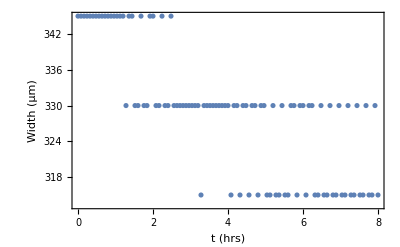

```mathematica
(* Width of ϕ profile *)
ϕL=0.2; ϕH=0.8;
ϕMid=Boole@Map[(ϕL<#)&& (#<ϕH)&,ϕAll, {2}];
AllWidths=Total[ϕMid]*ΔxSet;

width = Mean[ AllWidths[[Round[T/2];;]] ]
ListPlot[ Transpose[{tmesh,AllWidths}] , Frame-> True, FrameLabel->{"t (hrs)", "Width (μm)"}]
```

#### Plots

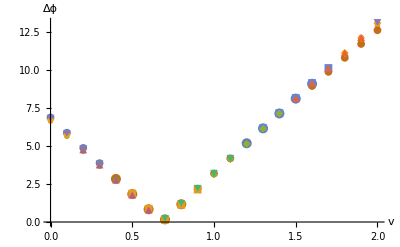

```mathematica
(* Plot difference between translated profiles *)
t1temp=ConstantArray[vpList, t1len ] ;
plotdata=Partition[  Transpose[ {Flatten@t1temp, Flatten@ΔϕFull} ] , t1len];hplot=ListPlot[plotdata, Frame->False, PlotMarkers->{Automatic, 8},AxesLabel->{Style["v",Black, FontSize-> 20],Style["Δϕ", Black,FontSize-> 20] }, TicksStyle->Directive[Black,16]]
```

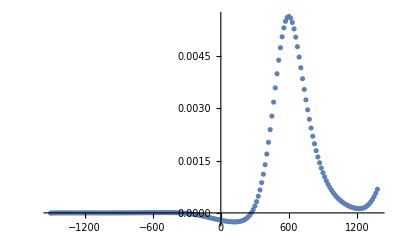

```mathematica
(* Plot difference between profiles given a certain shift *)
Module[{t1 = T1,dt = δt},
xvals = Table[xmesh[[xj]], {xj, 1, Nx-vInferred dt}];
δvals=Table[ϕAll[[x, t1 ]]-ϕAll[[x+vInferred dt, t1+dt]], {x, 1, Nx-vInferred dt}];
]
p1=ListPlot[Transpose[{xvals, δvals}],PlotRange-> All,PlotLegends->"Δϕ"]
```

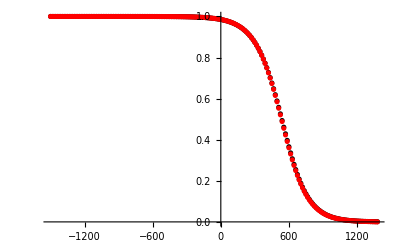

```mathematica
(* Plot both profiles given a certain shift *)
Module[{t1 = T1,dt = δt},
xvals = Table[xmesh[[xj]], {xj, 1, Nx-vInferred dt}];
ϕ1vals=Table[ϕAll[[x, t1 ]], {x, 1, Nx-vInferred dt}];
ϕ2vals=Table[ϕAll[[x+vInferred dt, t1+dt]], {x, 1, Nx-vInferred dt}];
]

p1=ListPlot[Transpose[{xvals, ϕ1vals}],PlotRange-> All,PlotLegends->"ϕ1", PlotStyle-> {Black}];
p2=ListPlot[Transpose[{xvals, ϕ2vals}],PlotRange-> All,PlotLegends->"ϕ2", PlotStyle-> {Red}];
Show[p1,p2]
```

### Wave characteristics vs parameters

```mathematica
(* Manually curate results *)  
(*
eMAll = {30, 10, 1, 100, 50, 300, 80, 90, 200, 100};
velocities = {127.5, 131.25, 131.25, 93.75, 131.25,  93.75, 131.25, 112.5, 112.5, 112.5};
widths = {16755/52, 16725/52, 4170/13, 12435/52, 16905/52, 8805/26,4230/13,4230/13,  8625/26, 8475/26};
*)
```

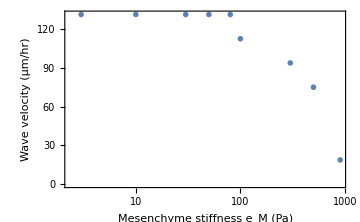

```mathematica
(* Plot velocities *)
plotdata = Transpose[{ paramsAll, velocities}] ;
(*p1=ListPlot[ plotdata ];*)
plotstyle= {LabelStyle-> {FontSize-> 16}, PlotMarkers->{Automatic, Scaled[0.04]} };
p1 =ListLogLinearPlot[plotdata, plotstyle];
Show[p1, Frame-> True, FrameLabel-> {"Mesenchyme stiffness e_M (Pa)","Wave velocity (μm/hr)"}, ImageSize-> Medium]
```

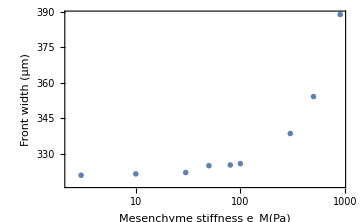

```mathematica
(* Plot widths *)
plotdata = Transpose[{ paramsAll, widths}] ;
(*p1=ListPlot[ plotdata, PlotRange->Full ];*)
p1 =ListLogLinearPlot[plotdata, PlotRange->Full, plotstyle];
Show[p1, Frame-> True, FrameLabel-> {"Mesenchyme stiffness e_M(Pa)","Front width (μm)"}, ImageSize-> Medium]
```